# PROJEKTNA NALOGA

SPLOŠNA MATURA MATEMATIKE - Izpitna pola 1, Sobota, 9. junij 2018 (2. naloga)

Spletna stran: https://www.ric.si/mma/M181-401-1-1/2018101013584229/

Na vsaki od spodnjih slik so paralelogrami ABCD ter vektorji a, b in v. Točke E, F in G so razpolovišča stranic, točka S pa presečišče diagonal. Pod vsakim paralelogramom zapišite
vektor v kot linearno kombinacijo vektorjev a in b.

1. Primer

```mathematica
Graphics[{Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{1/2,1/2}}],Arrow[{{1/2,1/2},{1,0}}],{Dashed,Line[{{1/2,1/2},{3/2,1/2}}],Line[{{3/2,1/2},{1,0}}]}}]
```

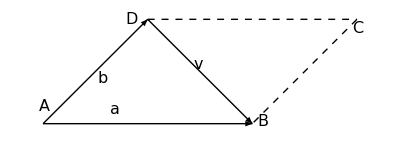

v=a-b

2. Primer

```mathematica
Graphics[{Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{1/2,1/2}}],Arrow[{{3/2,1/2},{1/2,0}}],{Dashed,Line[{{1/2,1/2},{3/2,1/2}}],Line[{{3/2,1/2},{1,0}}]}}]
```

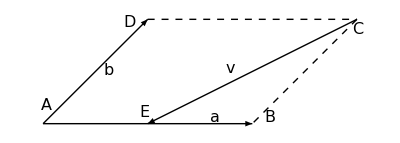

v=-1/2a-b

3. Primer

```mathematica
Graphics[{Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{1/2,1/2}}],Arrow[{{2/2,1/2},{5/4,1/4}}],{Dashed,Line[{{1/2,1/2},{3/2,1/2}}],Line[{{3/2,1/2},{1,0}}]}}]
```

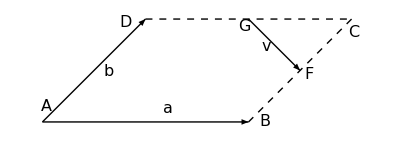

v=1/2 a-1/2 b

4. Primer

```mathematica
Graphics[{Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{1/2,1/2}}],Arrow[{{3/4,1/4},{1,0}}],{Dashed,Line[{{1/2,1/2},{3/2,1/2}}],Line[{{3/2,1/2},{1,0}}],Line[{{1/2,1/2},{3/4,1/4}}],Line[{{0,0},{3/2,1/2}}]}}]
```

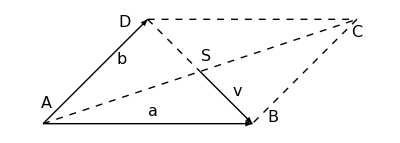

v=1/2 a-1/2 b

5. Primer

```mathematica
Graphics[{Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{1/2,1/2}}],Arrow[{{3/2,1/2},{0,0}}],{Dashed,Line[{{1/2,1/2},{3/2,1/2}}],Line[{{3/2,1/2},{1,0}}]}}]
```

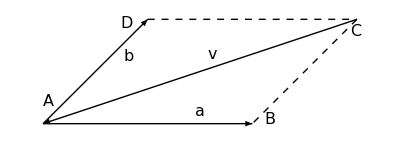

v=-a-b

LINEARNA ALGEBRA - Vaje 4 (3. naloga)

Podane imamo točke tristrane piramide A(2, 0, 0), B(0, 3, 0), C(0, 0, 6) in D(2, 3, 8). Izračunati je potrebno koliko znaša prostornina te piramide.

```mathematica
AA ={2,0,0};
BB={0,3,0};
CC={0,0,6};
DD={2,3,8};
TristranaPiramida=Tetrahedron[{{2,0,0},{0,3,0},{0,0,6},{2,3,8}}];
```

Za izračun prostornine je potrebno najti vektorje, ki med seboj niso koplanarni in se pričnejo v isti točki.

```mathematica
ClearAll[a,b]
```

```mathematica
a=BB-AA
```

{-2,3,0}

```mathematica
b=CC-AA
```

{-2,0,6}

```mathematica
c=DD-AA
```

{0,3,8}

```mathematica
produkt[a_,b_]:=Cross[a,b]
prostornina[a,b,c]:=1/6*produkt[a,b].c
```

```mathematica
prostornina[a,b,c]
```

14

```mathematica
Graphics3D[{{Opacity[0.6],LightBlue,TristranaPiramida}},Axes->True]
```

-Graphics3D-